{x1[0]==-0.2,x2[0]==-0.2,x1'[0]==-0.2,x2'[0]==-0.2}

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

{{x10, | },{x20, | },{v10, | },{v20, | }}

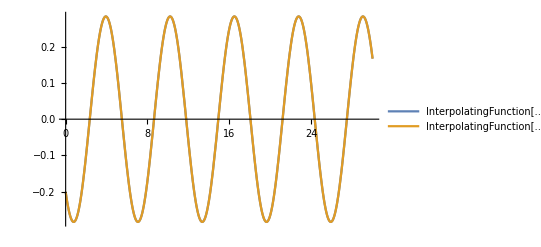

```mathematica
Clear[x1,x2,t]
rule={x1[0]==x10,x2[0]==x20,x1'[0]==v10,x2'[0]==v20}
sol=NDSolve[{-1(x1[t]-x2[t])-x1[t]==x1''[t],(x1[t]-x2[t])-x2[t]==x2''[t],rule},{x1,x2},{t,100}]
{{"x10",Slider[Dynamic[x10],{-.2,.2},Appearance->"Labeled"]},{"x20",Slider[Dynamic[x20],{-.2,.2},Appearance->"Labeled"]},{"v10",Slider[Dynamic[v10],{-.2,.2},Appearance->"Labeled"]},{"v20",Slider[Dynamic[v20],{-.2,.2},Appearance->"Labeled"]}}
Animate[Graphics[{{AbsoluteThickness[7],Gray,Line[{{0.9,2},{2.1,2}}]},{Blue,Line[{{{1,2},{1+First[Evaluate[x1[t]/.sol]],.5}},{{2,2},{2+First[Evaluate[x2[t]/.sol]],.5}}}]},{AbsoluteThickness[5],Red,Line[{{1+First[Evaluate[x1[t]/.sol]],.5},{2+First[Evaluate[x2[t]/.sol]],.5}}]},Disk[{1+First[Evaluate[x1[t]/.sol]],.5},0.1],Disk[{2+First[Evaluate[x2[t]/.sol]],.5},0.1]},Axes->True,AxesOrigin->{0,0},PlotRange->{{0,3},{0,2}}],{t,0,60,0.005},AnimationRate->3.5,AnimationRunning->False]
Plot[{Evaluate[x1[t]/.sol],Evaluate[x2[t]/.sol]},{t,0,30},PlotLegends->"Expressions"]
```